Saddlenode bifurcation at x=0;  The diverging arrows/streamlines are suggestive that x=0 is an unstable saddle node. This is a saddlenode bifurcation example.

{{x→-√μ},{x→√μ}}

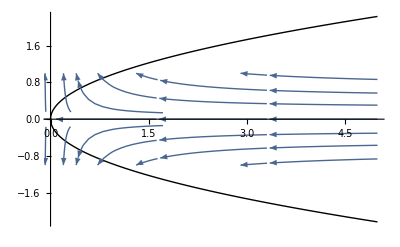

```mathematica
Clear[x,xdot,μ,y];
xdot=μ-x^2;
Solve[xdot==0,x]
μ=0.;
Plot[{μ-x^2},{x,-1,1}];
Show[Plot[{Sqrt[μ],-Sqrt[μ]},{μ,0,5},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{μ-x^2,y},{x,-5,5},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
μ=0.;
StreamPlot[{μ-x^2,y},{x,-5,5},{y,-1,1},GridLines->Automatic];
```

Two equilibrium equations exist: x=0 and x=μ.  When μ<0, the equilibrium is stable (streamlines move towards the equilibrium point).  When μ>0, the equilbrium is unstable (streamlines diverge or move away from the equilibrium point).  When μ=0, the equilibrium is unstable (the streamlines still move away from the equilibrium point, x=0).  This is known as a transcritical bifurcation at the parameter value, μ=0.  There is an “Exchange of stability” at μ=0.

{{x→0},{x→μ}}

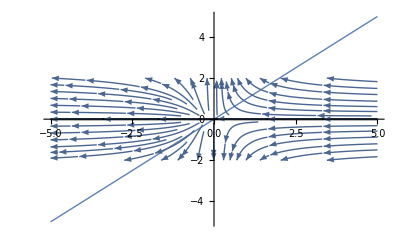

```mathematica
Clear[x,xdot,μ,y];
xdot=μ x-(x)^2;
Solve[xdot==0,x]
μ=0.;
Plot[{μ x-x^2},{x,-1,1},PlotStyle->{Thick,Black}];
Show[Plot[{μ,0},{μ,-5,5},PlotStyle->{Thick,Black}],
StreamPlot[{μ x-x^2,y},{x,-5,5},{y,-2,2},GridLines->Automatic,StreamScale->Medium]
]
```

Three equilibrium points exist at x=0, Sqrt[μ] and -Sqrt[μ].  Only at μ=0 is this equilibrium point stable (streamlines converge towards the equilibrium point).  At μ>0 and μ<0, the equilibrium point is unstable (streamlines diverge away from this point).

{{x→0},{x→-√μ},{x→√μ}}

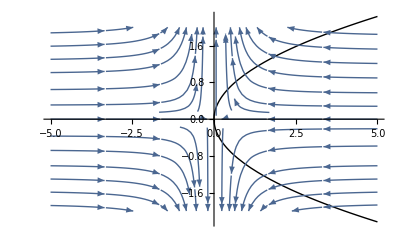

```mathematica
Clear[x,xdot,μ,y];
xdot=μ x-(x)^3;
Solve[xdot==0,x]
μ=0;
Plot[{μ x-x^2},{x,-1,1}];
Show[Plot[{Sqrt[μ],-Sqrt[μ]},{μ,-5,5},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{μ x-x^3,y},{x,-5,5},{y,-2,2},GridLines->Automatic,StreamScale->Medium]
]
```

The Lienhard equaton (which can be modified to the Van der Pol oscillator) is used next.  The phase portrait and the streamplot at μ=-0.3 suggest a stable focal point (streamlines converge into the focal point).  For a μ=1.0, the focal point is unstable (streamlines diverge away from the focal point).  The focal point, in this case is the origin.  This is an example of the Hopf bifurcation.

InterpolatingFunction[{{0., 80.}}, <>]

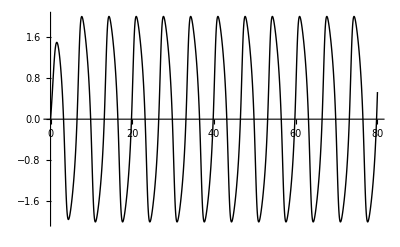

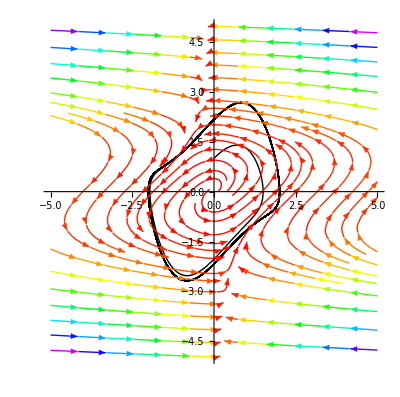

```mathematica
Clear[μ,s,x,t,tmax];
μ=1;tmax=80;
s=NDSolveValue[{x''[t]-(μ-x[t]^2)x'[t]+x[t]==0,x[0]==0,x'[0]==1},x,{t,0,tmax}]
Plot[s[t],{t,0,tmax},PlotStyle->{Thick,Black},PlotRange->All]
Show[
ParametricPlot[{s[t],s'[t]},{t,0,tmax},PlotStyle->{Thick,Black},PlotRange->All],
StreamPlot[{-u+(μ-u^2)v,v},{v,-5,5},{u,-5,5},StreamColorFunction->Hue,StreamPoints->40]
]
```

The Van der Pol oscillator is next used.  For a “highly nonlinear” problem (ϵ=0.99), the vdp oscillator describes an unstable focal point.  For a “weakly nonlinear” problem with (ϵ=0.1), the focal point is stable.  This is a Hopf bifurcation example, again.

InterpolatingFunction[{{0., 10.}}, <>]

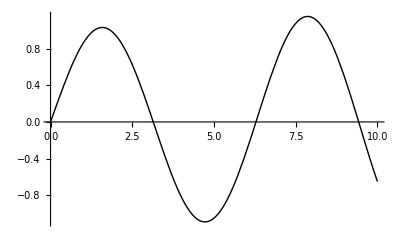

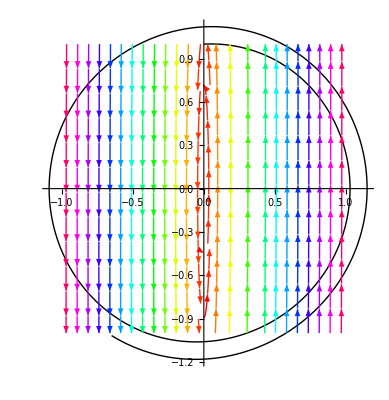

```mathematica
Clear[μ,s,x,t,tmax];
ϵ=0.05;tmax=10;
s=NDSolveValue[{x''[t]-ϵ(1-x[t]^2)x'[t]+x[t]==0,x[0]==0,x'[0]==1},x,{t,0,tmax}]
Plot[s[t],{t,0,tmax},PlotStyle->{Thick,Black},PlotRange->All]
Show[
ParametricPlot[{s[t],s'[t]},{t,0,tmax},PlotStyle->{Thick,Black},PlotRange->All],
StreamPlot[{ϵ (x-(x^3/3)-y),x/ϵ},{x,-1,1},{y,-1,1},StreamColorFunction->Hue,StreamPoints->40]
]
```